# Fabry Perot Dark Offset Tutorial Solutions

## Part 1: Transmitted Power

#### Define the transmitted field function (assuming Ein = 1 √W)

```mathematica
Etrans[ϕ_,t1_:0.3,t2_:0.3,r1_:√(1-0.3^2),r2_:√(1-0.3^2)]:=(t1 t2 Exp[-I ϕ])/(1-r1 r2 Exp[-I 2 ϕ]);
```

#### 1. Derive an expression for the transmitted power P_trans(ϕ)

```mathematica
Etrans0=Etrans[ϕ,t1,t2,r1,r2];
Ptrans=Simplify[ComplexExpand[Etrans0 Conjugate[Etrans0]]]
```

(t1^2 t2^2)/(1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ])

#### 2. What is the maximum transmitted power at resonance P_trans(0)?

```mathematica
Ptrans/.{ϕ->0}
```

(t1^2 t2^2)/(1-2 r1 r2+r1^2 r2^2)

#### 3. Starting at resonance, what happens to P_trans when the cavity gets longer?

The power goes down like ϕ^2.  
Looking at the equation for P_trans, the cosine in the denominator ensures that the offset must be significant before we start to see change.
Quantitatively, we could take the derivative of P_trans with respect to ϕ, then evaluate at ϕ = 0

```mathematica
dPtransdϕ=Simplify[D[Ptrans,ϕ]]
```

-(4 r1 r2 t1^2 t2^2 Sin[2 ϕ])/((1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ])^2)

```mathematica
dPtransdϕ/.{ϕ->0}
```

0

#### 4. Starting at resonance, what happens to P_trans when the cavity gets shorter?

Again, the power goes down like ϕ^2.  
This is equivalent because the P_trans function is symmetric.  If one considers ϕ → -ϕ in the P_trans function, we get the same value as before because Cos[-ϕ] = Cos[ϕ]

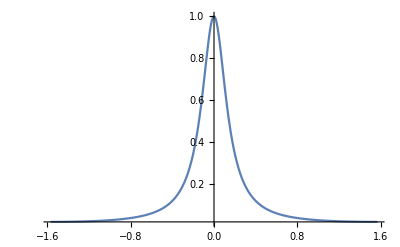

```mathematica
Plot[Ptrans//.{r2->r1,t2->t1,r1->√(1-t1^2),t1->0.5},{ϕ,-π/2,π/2},PlotRange->Full]
```

#### 5. Would it be possible to use the transmitted power to restore resonance in case of some disturbance ΔL?

Perhaps.  
You would have to move in a direction and monitor whether the transmitted power went up or down.  
If transmitted power went down, then you’d need to switch directions.  
It would be hard to know when you achieved perfect resonance as well, as you’d tend to go past it and need to reverse directions.

#### Extra Credit: Transmitted Field Phasor Plots

We get two “lobes” for even and odd resonances, thanks to the Exp[-I ϕ] in the numerator.

```mathematica
Manipulate[Show[{ParametricPlot[{Re[Etrans[ϕ]],Im[Etrans[ϕ]]},{ϕ,0,2π},PlotRange->{-1,1},PlotPoints->200,MaxRecursion->10],
ListLinePlot[{{0,0},{Re[Etrans[ϕ0]],Im[Etrans[ϕ0]]}},PlotStyle->{Thickness[0.01],Red},PlotLegends->{"carrier ω0"}]
}],
{ϕ0,0,2π},Paneled->False]
```

## Part B: Reflected Power

#### Define the REFL electric field

```mathematica
Erefl[ϕ_,t1_:0.3,t2_:0.3,r1_:√(1-0.3^2),r2_:√(1-0.3^2)]:=(r1-r2 Exp[-I 2 ϕ])/(1-r1 r2 Exp[-I 2 ϕ]);
```

```mathematica
Manipulate[Show[{ParametricPlot[{Re[Erefl[ϕ]],Im[Erefl[ϕ]]},{ϕ,0,2π},PlotRange->{-1,1},PlotPoints->200,MaxRecursion->10],
ListLinePlot[{{0,0},{Re[Erefl[ϕ0]],Im[Erefl[ϕ0]]}},PlotStyle->{Thickness[0.01],Red},PlotLegends->{"carrier ω0"}]
}],
{ϕ0,0,2π},Paneled->False]
```

#### 1. Derive an expression for the reflected power P_refl(ϕ). What is the reflected power at resonance?

```mathematica
Erefl0=Erefl[ϕ,t1,t2,r1,r2]
```

(r1-ⅇ^(-2 ⅈ ϕ) r2)/(1-ⅇ^(-2 ⅈ ϕ) r1 r2)

```mathematica
Prefl=Simplify[ComplexExpand[Erefl0 Conjugate[Erefl0]]]
```

(r1^2+r2^2-2 r1 r2 Cos[2 ϕ])/(1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ])

```mathematica
Simplify[Prefl/.{ϕ->0}]
```

(r1-r2)^2/(-1+r1 r2)^2

#### 2. Set r_2=r_1=r. Does P_refl(ϕ) simplify at all? What value do you get at resonance?

We get zero reflected power for a critically-coupled cavity at resonance.

```mathematica
Prefl2=Simplify[Prefl/.{r2->r,r1->r}]
```

(4 r^2 Sin[ϕ]^2)/(1+r^4-2 r^2 Cos[2 ϕ])

```mathematica
Prefl2/.{ϕ->0}
```

0

#### 3. Starting at resonance, what happens to the reflected power when the cavity gets longer? Shorter?

Here, the reflected power goes up like ϕ^2 for both the cavity getting longer and shorter, which can again be seen from the symmetric P_refl(ϕ) function.

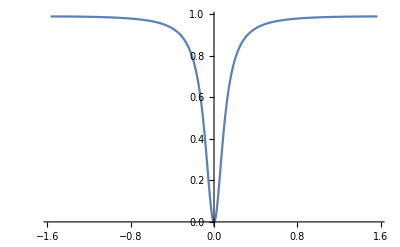

```mathematica
Plot[Prefl2/.{r->0.9},{ϕ,-π/2,π/2},PlotRange->Full]
```

#### 4. Can you use reflected power to restore resonance?

You would run into the same problems as for the transmitted power.

## Part C: The Reflected Field

#### 1. Derive an expression for the change in reflected field with respect to phase ϕ: dE_refl/dϕ(ϕ).

```mathematica
D[Erefl0,ϕ]
```

-(2 ⅈ ⅇ^(-2 ⅈ ϕ) r1 r2 (r1-ⅇ^(-2 ⅈ ϕ) r2))/((1-ⅇ^(-2 ⅈ ϕ) r1 r2)^2)+(2 ⅈ ⅇ^(-2 ⅈ ϕ) r2)/(1-ⅇ^(-2 ⅈ ϕ) r1 r2)

```mathematica
dErefl0dϕ=Simplify[D[Erefl0,ϕ]]
```

-(2 ⅈ ⅇ^(2 ⅈ ϕ) (-1+r1^2) r2)/((ⅇ^(2 ⅈ ϕ)-r1 r2)^2)

#### 2. Set r_2=r_1=r. What is E_refl(0)? What is dE_refl/dϕ(0)?

```mathematica
Simplify[Erefl0/.{r2->r,r1->r,ϕ->0}]
```

0

```mathematica
Simplify[dErefl0dϕ/.{r2->r,r1->r}]
```

-(2 ⅈ ⅇ^(2 ⅈ ϕ) r (-1+r^2))/((ⅇ^(2 ⅈ ϕ)-r^2)^2)

```mathematica
Simplify[dErefl0dϕ/.{r2->r,r1->r,ϕ->0}]
```

-(2 ⅈ r)/(-1+r^2)

Again, E_refl(0)=0, but dE_refl/dϕ(0) = (2 i r)/(1-r^2).  
So we have no reflected field returning in reflection exactly at resonance, but the field is moving rapidly in the imaginary direction at resonance.

#### 3. What happens to the reflected field when the cavity gets longer? What about shorter?

If we think about a field Taylor expansion about resonance, to first order we get 
E_refl(ϕ)|_(ϕ→0) =  E_refl(0)+ϕ dE_refl/dϕ(0) = ϕ(2 i r)/(1-r^2).
This means that the field is becomes positive imaginary when the cavity gets longer (ϕ > 0),
but becomes negative imaginary when the cavity gets shorter (ϕ < 0).
So we’ve finally recovered something which changes linearly with phase.

#### 4. Could you use the reflected field to restore resonance? What would you need in order to do so?

We can’t measure the reflected electric field directly unfortunately.  
When we tried to measure the power, we got something that scaled like ϕ^2, which wasn’t that useful.

We would need a local oscillator to measure E_refl directly.
A local oscillator is just a reference electric field that interferes with our signal field.  
We will explore one option for creating a local oscillator below.

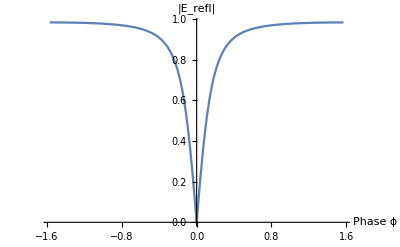

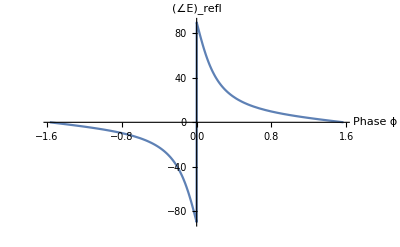

```mathematica
Plot[Abs[Erefl0//.{r2->r1,r1->√(1-0.3)}],{ϕ,-π/2,π/2},PlotRange->Full,AxesLabel->{"Phase ϕ","|E_refl|"}]
Plot[180/π Arg[Erefl0//.{r2->r1,r1->√(1-0.3)}],{ϕ,-π/2,π/2},PlotRange->Full,AxesLabel->{"Phase ϕ","(∠E)_refl"}]
```

## Part 4. Dither Locking

#### 1. First, find the transfer function from the end mirror E_cav2 to the reflected field E_refl.

E_refl=r_1 E_in+t_1 e^(-i ϕ)E_cav2, but we are only focused on the contribution to E_refl from E_cav2, so we set E_in=0

E_refl/E_cav2=t_1 e^(-i ϕ)E_cav2/E_cav2

Remember that E_cav2/E_cav2= 1/(1-r_1 r_2 Exp[-i 2 ϕ]) is the cavity loop suppression: E_cav2 has to go around the loop to get back to itself.
This yields our final answer:

E_refl/E_cav2=(t_1 e^(-i ϕ))/(1-r_1 r_2 e^(-i 2ϕ))

```mathematica
Ecav2toErefl[ϕ_]:=(t1 Exp[-I ϕ])/(1-r1 r2 Exp[-I 2ϕ]);
```

#### 2. Find the carrier field incident on the end mirror.

Incident on the end mirror will be E_cav/E_in=t_1/(1-r_1 r_2 e^(-i 2ϕ))times the propagation to the back mirror e^(-i ϕ).

```mathematica
Ecavend=(t1 Exp[-I ϕ])/(1-r1 r2 Exp[-I 2ϕ]);
```

#### 3. Apply the length modulation Δx cos(ω t) to find the total field immediately reflected off the end mirror E_cav2. Hint: There should be three fields.

We apply the modulation to the E_cavend carrier field
E_cav2=(1+i k Δx e^(i ω t)+i k Δx e^(-i ω t)) r_2 E_cavend

I’ll split the fields explicitly like
E_cav2 = E_(cav2,0)+E_(cav2,usb)+E_(cav2,lsb)

```mathematica
Ecav20=r2 Ecavend
Ecav2usb=I k Δx r2 Ecavend Exp[I ω t]
Ecav2lsb=I k Δx r2 Ecavend Exp[-I ω t]
```

(ⅇ^(-ⅈ ϕ) r2 t1)/(1-ⅇ^(-2 ⅈ ϕ) r1 r2)

(ⅈ ⅇ^(-ⅈ ϕ+ⅈ t ω) k r2 t1 Δx)/(1-ⅇ^(-2 ⅈ ϕ) r1 r2)

(ⅈ ⅇ^(-ⅈ ϕ-ⅈ t ω) k r2 t1 Δx)/(1-ⅇ^(-2 ⅈ ϕ) r1 r2)

#### 4. Apply your transfer function from (1) to your E_cav2 to find the total reflected field. Hint: It may be easier to consider the accrued phases for carrier ϕ and for the audio sidebands ϕ ± η

First, I clarify what the phases ϕ and η are.  

ϕ = k L = (ω_0 L)/c is the phase accrued by the carrier as it passes through the cavity.  Here ω_0 is the carrier frequency.

η = (ω L)/c is the additional phase accrued by the upper sideband (or phase subtracted for the lower sideband) as they pass through the cavity.

The key is, all the beams experience the same cavity length L, but have a different frequency.  
This causes the fields to accrue a different phase as they pass through the cavity.

So, to find the carrier contribution to E_refl, we simply do the usual transfer function E_refl/E_in at the same phase ϕ.
But for the upper and lower sideband contributions to E_refl, we need to apply E_refl/E_cav2at ϕ ± η to our carrier TF that got us to the end mirror:

Carrier: E_(refl,0)=E_refl/E_in(ϕ)E_in
Upper Sideband: E_(refl,usb)=E_refl/E_cav2(ϕ+η) E_cav2/E_in(ϕ)E_in
Lower Sideband: E_(refl,lsb)=E_refl/E_cav2(ϕ-η)E_cav2/E_in(ϕ) E_in

For the sideband terms, we get a product of the carrier resonance experienced in the cavity, building up to high field strength, and the sideband term itself, which can also resonant inside the cavity

```mathematica
Erefl00=Erefl0 
Ereflusb=Ecav2usb Ecav2toErefl[ϕ+η]
Erefllsb=Ecav2lsb Ecav2toErefl[ϕ+η]

Erefltotal=(Erefl00+Ereflusb+Erefllsb)E0 Exp[I ω0 t]
```

(r1-ⅇ^(-2 ⅈ ϕ) r2)/(1-ⅇ^(-2 ⅈ ϕ) r1 r2)

(ⅈ ⅇ^(-ⅈ ϕ-ⅈ (η+ϕ)+ⅈ t ω) k r2 t1^2 Δx)/((1-ⅇ^(-2 ⅈ ϕ) r1 r2) (1-ⅇ^(-2 ⅈ (η+ϕ)) r1 r2))

(ⅈ ⅇ^(-ⅈ ϕ-ⅈ (η+ϕ)-ⅈ t ω) k r2 t1^2 Δx)/((1-ⅇ^(-2 ⅈ ϕ) r1 r2) (1-ⅇ^(-2 ⅈ (η+ϕ)) r1 r2))

ⅇ^(ⅈ t ω0) E0 ((r1-ⅇ^(-2 ⅈ ϕ) r2)/(1-ⅇ^(-2 ⅈ ϕ) r1 r2)+(ⅈ ⅇ^(-ⅈ ϕ-ⅈ (η+ϕ)-ⅈ t ω) k r2 t1^2 Δx)/((1-ⅇ^(-2 ⅈ ϕ) r1 r2) (1-ⅇ^(-2 ⅈ (η+ϕ)) r1 r2))+(ⅈ ⅇ^(-ⅈ ϕ-ⅈ (η+ϕ)+ⅈ t ω) k r2 t1^2 Δx)/((1-ⅇ^(-2 ⅈ ϕ) r1 r2) (1-ⅇ^(-2 ⅈ (η+ϕ)) r1 r2)))

#### 5. Calculate the total reflected power P_refl(t). Let Δx^2→0 for small length modulations.

This is a lot of algebra, and it can be easier to let Mathematica handle it.
Letting Mathematica do the heavy lifting

```mathematica
Prefltotal=Simplify[ComplexExpand[Erefltotal Conjugate[Erefltotal]]];
Prefltotal=FullSimplify[Prefltotal/.{Δx^2->0}];
Preflcollect=Collect[Prefltotal,Δx](*DC term on the Left*)
```

(E0^2 (r1^2+r2^2-2 r1 r2 Cos[2 ϕ]))/(1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ])+(4 E0^2 k r2 t1^2 Δx Cos[t ω] ((-1+r1^2) r2 Sin[η]-r1 (-1+r2^2) Sin[η+2 ϕ]))/((1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ]) (1+r1^2 r2^2-2 r1 r2 Cos[2 (η+ϕ)]))

However, we can also try to be clever, and develop our intuition, 
by leaving the fields in their general form:
(below I have incorporated the imaginary term i into the E-fields to be consistent with our Mathematica definitions.)

E_refl=E_(refl,0)+k Δx E_(refl,usb) e^(i ω t)+k Δx E_(refl,lsb)e^(-i ω t)

P_refl(t)= P_(refl,DC)+P_(refl,1ω)(t)

P_(refl,DC)=|E_(refl,0)|^2+(k Δx)^2|E_(refl,usb)|^2+(k Δx)^2|E_(refl,lsb)|^2

P_(refl,1ω)(t)=k Δx P_in (e^(i ω t)((E_(refl,0))^*E_(refl,usb)+E_(refl,0)(E_(refl,lsb))^*)+e^(-i ω t)(E_(refl,0)(E_(refl,usb))^*+(E_(refl,0))^*E_(refl,lsb)))

In the last term P_(refl,1ω)(t), we get our oscillations at frequency ω.  
The term on the right inside the parentheses is just the complex conjugate of the term on the left.
So we could do something like write z(t)=e^(i ω t)((E_(refl,0))^*E_(refl,usb)+E_(refl,0)(E_(refl,lsb))^*), and get 

P_(refl,1ω)(t)=k Δx (e^(i ω t)((E_(refl,0))^*E_(refl,usb)+E_(refl,0)(E_(refl,lsb))^*)+CC)
P_(refl,1ω)(t)=k Δx (z+z^*)
P_(refl,1ω)(t)=2k Δx Re(z)
P_(refl,1ω)(t)=2k Δx Re(e^(i ω t)((E_(refl,0))^*E_(refl,usb)+E_(refl,0)(E_(refl,lsb))^*))

If we calculate this term in the parenthesis:

```mathematica
zz=Simplify[ComplexExpand[Conjugate[Erefl00]Ereflusb+Erefl00 Conjugate[Erefllsb]]]
```

-(2 k r2 t1^2 Δx (-((-1+r1^2) r2 Sin[η])+r1 (-1+r2^2) Sin[η+2 ϕ]) (Cos[t ω]+ⅈ Sin[t ω]))/((1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ]) (1+r1^2 r2^2-2 r1 r2 Cos[2 (η+ϕ)]))

```mathematica
Simplify[ComplexExpand[Re[zz]]]
```

-(2 k r2 t1^2 Δx Cos[t ω] (-((-1+r1^2) r2 Sin[η])+r1 (-1+r2^2) Sin[η+2 ϕ]))/((1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ]) (1+r1^2 r2^2-2 r1 r2 Cos[2 (η+ϕ)]))

```mathematica
Prefl1ω=Simplify[2 E0^2 Simplify[ComplexExpand[Re[zz]]]]
```

-(4 E0^2 k r2 t1^2 Δx Cos[t ω] (-((-1+r1^2) r2 Sin[η])+r1 (-1+r2^2) Sin[η+2 ϕ]))/((1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ]) (1+r1^2 r2^2-2 r1 r2 Cos[2 (η+ϕ)]))

Compare Prefl1ω to the second term in Prefltotal, and we get the same result

```mathematica
Preflcollect[[2]]
```

(4 E0^2 k r2 t1^2 Δx Cos[t ω] ((-1+r1^2) r2 Sin[η]-r1 (-1+r2^2) Sin[η+2 ϕ]))/((1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ]) (1+r1^2 r2^2-2 r1 r2 Cos[2 (η+ϕ)]))

```mathematica
Simplify[Preflcollect[[2]]/Prefl1ω]
```

1

#### 6. Demodulate the power signal

This appears to be another monumental algebraic task, and it is.
Again, let’s start by letting Mathematica do the heavy lifting.

```mathematica
PrefltotaldemodI=Simplify[1/(2π)Integrate[Prefltotal Cos[ωt]/.{t->-ωt/ω},{ωt,0,2π}]]
PrefltotaldemodQ=Simplify[1/(2π)Integrate[Prefltotal Sin[ωt]/.{t->-ωt/ω},{ωt,0,2π}]]
Prefltotaldemodtf=(PrefltotaldemodI+I PrefltotaldemodQ)/Δx
```

(2 E0^2 k r2 t1^2 Δx ((-1+r1^2) r2 Sin[η]-r1 (-1+r2^2) Sin[η+2 ϕ]))/((1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ]) (1+r1^2 r2^2-2 r1 r2 Cos[2 (η+ϕ)]))

0

(2 E0^2 k r2 t1^2 ((-1+r1^2) r2 Sin[η]-r1 (-1+r2^2) Sin[η+2 ϕ]))/((1+r1^2 r2^2-2 r1 r2 Cos[2 ϕ]) (1+r1^2 r2^2-2 r1 r2 Cos[2 (η+ϕ)]))

```mathematica
Solve[Prefltotaldemodtf==0,Sin[η+2 ϕ]]
```

{{Sin[η+2 ϕ]→((-1+r1^2) r2 Sin[η])/(r1 (-1+r2^2))}}

So we retrieve half the 1ω power signal in I, and nothing in the Q quadrature.  
Forming the length to reflected power transfer function at ω is as simple as dividing by Δx, as we did in the final step.

This can be seen by analyzing Prefl1ω above.  
It has only a Cos[ω t] term, which indicates which quadrature we’ll find our signal in (the I-quadrature).

Again, by being a bit clever we can simplify our calculations.
Starting again with the generalized term:

P_(refl,1ω)(t)=2k Δx Re(z)
with z=e^(i ω t)((E_(refl,0))^*E_(refl,usb)+E_(refl,0)(E_(refl,lsb))^*)

We can try to directly demodulate this expression.

P_(refl,I)=1/(2π)(∫_0)^(2π)P_(refl,1ω)(t)cos(ωt)d(ωt)
P_(refl,Q)=1/(2π)(∫_0)^(2π)P_(refl,1ω)(t)sin(ωt)d(ωt)

If I set z = y e^(i ω t), where y=(E_(refl,0))^*E_(refl,usb)+E_(refl,0)(E_(refl,lsb))^*, 
then it becomes exquisitely clear what we are measuring when we do the demodulation

```mathematica
II=1/(2π)Integrate[ComplexExpand[Re[y Exp[I ωt]]Cos[ωt],y],{ωt,0,2π}]
QQ=1/(2π)Integrate[ComplexExpand[Re[y Exp[I ωt]]Sin[ωt],y],{ωt,0,2π}]
II + I QQ
TF=FullSimplify[II + I QQ]
```

Re[y]/2

-Im[y]/2

-1/2 ⅈ Im[y]+Re[y]/2

Conjugate[y]/2

By using modulating the end mirror with a length change Δx cos(ω t), 
and then demodulating at that same frequency ω, 
we are picking off a product of our electric fields y=(E_(refl,0))^*E_(refl,usb)+E_(refl,0)(E_(refl,lsb))^*.

What’s more, that product of electric fields is incredibly useful for our ultimate goal: maintaining resonance by detecting the phase of light via a power signal.
Essentially, encoded into the power signal P_refl(t) at the frequency ω is our phase signal from E_refl, which can be used to hold onto resonance.

#### Plot of Dither Locking Phase Sweep

Let’s plot a phase sweep of our demodulated cavity length to reflected power transfer function P_refl/Δx(ω,ϕ) 
for some low frequency signal, say ω = 2π (100 Hz) for some cavity length L = 1 meter.
We’ll assume some moderate finesse cavity, with equal transmissions T_1=T_2=0.3.

Parameters for substitution into our function

```mathematica
params={E0->1,k->(2π)/λ,ω->2π f,η->(ω L)/c,r1->√(1-T1),r2->√(1-T2),t1->√T1,t2->√T2};
values={λ->1064 10^-9,T1->0.3,T2->0.3,L->1,c->3 10^8,f->10000};
```

```mathematica
(*Prefltotaldemodtf//.params/.values*)
```

Plot of our demodulated function P_refl/Δx(ω,ϕ) over ϕ

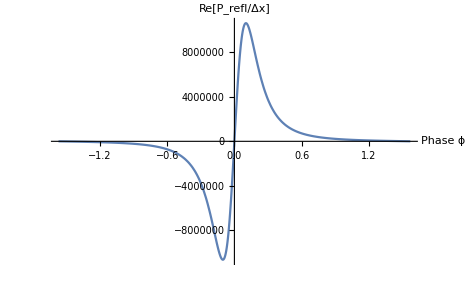

```mathematica
zoom=1;
Plot[Re[Prefltotaldemodtf//.params/.values],{ϕ,-zoom π/2,zoom π/2},PlotRange->Full,AxesLabel->{"Phase ϕ","Re[P_refl/Δx]"}]
(*Plot[Im[Prefltotaldemodtf//.params/.values],{ϕ,-π/2,π/2},PlotRange->Full,AxesLabel->{"Phase ϕ","Im[P_refl/Δx]"}]*)
```

Interpreting the above plot, we get a zero crossing of our reflected power signal P_refl coming from our end-mirror modulation Δx directly at resonance where ϕ = 0.
The y-axis units are in watts per meter, and tell us ultra-sensitive our interferometer is to end-mirror motion near resonance, even for this low-performing interferometer..

Comparing to the real and imaginary plots of E_refl sweep over ϕ.
Notice that our real demodulated signal P_refl/Δx(ω,ϕ)  is very similar to our imaginary part of E_refl

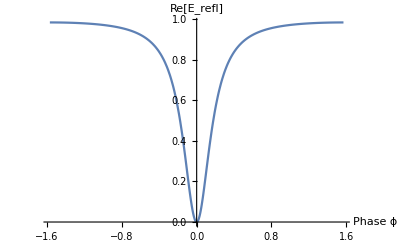

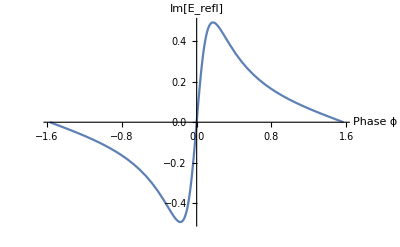

```mathematica
Plot[Re[Erefl0//.{r2->r1,r1->√(1-0.3)}],{ϕ,-π/2,π/2},PlotRange->Full,AxesLabel->{"Phase ϕ","Re[E_refl]"}]
Plot[Im[Erefl0//.{r2->r1,r1->√(1-0.3)}],{ϕ,-π/2,π/2},PlotRange->Full,AxesLabel->{"Phase ϕ","Im[E_refl]"}]
```

#### Plot of Dither Locking Transfer Function

Here we adjust the dither frequency ω, while assuming we are perfectly on resonance. 
This gives us our length-to-reflected-power transfer function frequency response.

This time our values need to specify our carrier phase ϕ, not our modulation frequency ω which we want to sweep.
We specify the carrier phase ϕ = 1°, because if we are at exactly ϕ = 0° our error signal goes to zero (as seen in our phase sweep above).

```mathematica
values2={λ->1064 10^-9,T1->0.3,T2->0.3,L->1,c->3 10^8,ϕ->1 π/180};
flow=10^4;
fhigh=3 10^8;
```

```mathematica
Prefltotaldemodtf//.params
```

(4 π T1 √(1-T2) (-T1 √(1-T2) Sin[(2 f L π)/c]+√(1-T1) T2 Sin[(2 f L π)/c+2 ϕ]))/(λ (1+(1-T1) (1-T2)-2 √(1-T1) √(1-T2) Cos[2 ϕ]) (1+(1-T1) (1-T2)-2 √(1-T1) √(1-T2) Cos[2 ((2 f L π)/c+ϕ)]))

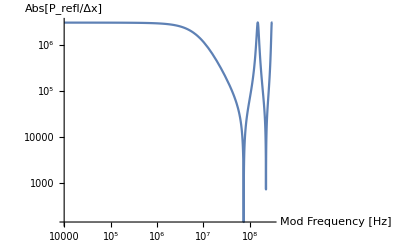

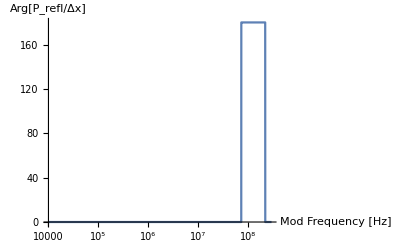

```mathematica
LogLogPlot[Abs[Prefltotaldemodtf//.params/.values2],{f,flow,fhigh},PlotRange->Full,AxesLabel->{"Mod Frequency [Hz]","Abs[P_refl/Δx]"}]
LogLinearPlot[180/π Arg[Prefltotaldemodtf//.params/.values2],{f,flow,fhigh},PlotRange->Full,AxesLabel->{"Mod Frequency [Hz]","Arg[P_refl/Δx]"}]
```